## Analytical Slope by WOS: f_1, g_1, f_2, g_2

```mathematica
(* This ODE system corresponds to PG3 with anzats z=x-ct *)
odeP=c*P'[z]+α*P[z]*(1-P[z]-M[z])-(qm+μ)*P[z]+qp*M[z];(* ==0 *)
odeM=c*M'[z]+Dv*M''[z]-qp*M[z]+qm*P[z];(* ==0 *)
(* We let ξ=ᾱ z. => P[z_]=f[ξ[z]]; M[z_]=g[ξ[z]]; etc
 We look for solutions of the following form *)
f[ξ_]=Subscript[f, 0][ξ]+ᾱ*Subscript[f, 1][ξ]+1/2*ᾱ^2*Subscript[f, 2][ξ]+1/6*ᾱ^3*Subscript[f, 3][ξ];
g[ξ_]=Subscript[g, 0][ξ]+ᾱ*Subscript[g, 1][ξ]+1/2*ᾱ^2*Subscript[g, 2][ξ]+1/6*ᾱ^3*Subscript[f, 3][ξ];
(* new system is derived by hand by hand*)
Print["---------- New ODE system -------------------"]
odeP=ᾱ*c*f'[ξ]+ᾱ*f[ξ]-α*f[ξ]*(f[ξ]+g[ξ])-qm*f[ξ]+qp*g[ξ];
odeM=ᾱ*c*g'[ξ]+ᾱ^2*Dv*g''[ξ]-qp*g[ξ]+qm*f[ξ];
odeP==0
odeM==0
Print["---------- Finding coefficients of ᾱ -------------------"]
coeffP=CoefficientList[odeP,ᾱ]
coeffM=CoefficientList[odeM,ᾱ]
Print["----------O(1)==0--------------"]
coeffM[[1]]==0
coeffP[[1]]==0
Solve[{coeffP[[1]]==0,coeffM[[1]]==0},{Subscript[f, 0][ξ],Subscript[g, 0][ξ]}]
Print["----------O(ᾱ)==0--------------"]
Subscript[f, 0][ξ_]=0; Subscript[g, 0][ξ_]=0; (* Result from O(1)==0 *)
coeffM[[2]]==0
coeffP[[2]]==0
Solve[{coeffP[[2]]==0,coeffM[[2]]==0},{Subscript[f, 1][ξ],Subscript[g, 1][ξ]}]
Print["----------O(ᾱ^2)==0--------------"]
Subscript[g, 1][ξ_]=qm *Subscript[f, 1][ξ]/qp; (* Result from O(ᾱ)==0 *)
coeffM[[3]]==0
coeffP[[3]]==0
Print["----------O(ᾱ^2)==0--------Solving DE------"]
de=Simplify[coeffP[[3]]+coeffM[[3]]]
Solve[de==0,Subscript[f, 1]'[ξ]]
Simplify[DSolve[{de==0,Subscript[f, 1][0]==1/(2*α)/(1+qm/qp)},Subscript[f, 1][ξ],ξ]]

Print["----------O(ᾱ^3)==0--------------"]
Subscript[f, 1][ξ_]=qp/((1+ⅇ^((qp ξ)/(c (qm+qp)))) (qm+qp) α); (* Result from O(ᾱ^2)==0 *)
Subscript[g, 2][ξ_]=(qm qp Subscript[f, 2][ξ]+2 c qm Subscript[f, 1]'[ξ])/qp^2;(* Given in equation from O(ᾱ^2)==0 *)
coeffP[[4]]==0
coeffM[[4]]==0
de2=Simplify[coeffP[[4]]+coeffM[[4]]];
de2==0
Simplify[DSolve[{de2==0,Subscript[f, 2][0]==0},Subscript[f, 2][ξ],ξ]]
Quit[](* Clear ALL definitions, including functions*)
```

---------- New ODE system -------------------

-qm (f_0[ξ]+ᾱ f_1[ξ]+1/2 (ᾱ)^2 f_2[ξ]+1/6 (ᾱ)^3 f_3[ξ])+ᾱ (f_0[ξ]+ᾱ f_1[ξ]+1/2 (ᾱ)^2 f_2[ξ]+1/6 (ᾱ)^3 f_3[ξ])+qp (1/6 (ᾱ)^3 f_3[ξ]+g_0[ξ]+ᾱ g_1[ξ]+1/2 (ᾱ)^2 g_2[ξ])-α (f_0[ξ]+ᾱ f_1[ξ]+1/2 (ᾱ)^2 f_2[ξ]+1/6 (ᾱ)^3 f_3[ξ]) (f_0[ξ]+ᾱ f_1[ξ]+1/2 (ᾱ)^2 f_2[ξ]+1/3 (ᾱ)^3 f_3[ξ]+g_0[ξ]+ᾱ g_1[ξ]+1/2 (ᾱ)^2 g_2[ξ])+c ᾱ (f_0'[ξ]+ᾱ f_1'[ξ]+1/2 (ᾱ)^2 f_2'[ξ]+1/6 (ᾱ)^3 f_3'[ξ])==0

qm (f_0[ξ]+ᾱ f_1[ξ]+1/2 (ᾱ)^2 f_2[ξ]+1/6 (ᾱ)^3 f_3[ξ])-qp (1/6 (ᾱ)^3 f_3[ξ]+g_0[ξ]+ᾱ g_1[ξ]+1/2 (ᾱ)^2 g_2[ξ])+c ᾱ (1/6 (ᾱ)^3 f_3'[ξ]+g_0'[ξ]+ᾱ g_1'[ξ]+1/2 (ᾱ)^2 g_2'[ξ])+Dv (ᾱ)^2 (1/6 (ᾱ)^3 f_3''[ξ]+g_0''[ξ]+ᾱ g_1''[ξ]+1/2 (ᾱ)^2 g_2''[ξ])==0

---------- Finding coefficients of ᾱ -------------------

{-qm f_0[ξ]-α f_0[ξ]^2+qp g_0[ξ]-α f_0[ξ] g_0[ξ],f_0[ξ]-qm f_1[ξ]-2 α f_0[ξ] f_1[ξ]-α f_1[ξ] g_0[ξ]+qp g_1[ξ]-α f_0[ξ] g_1[ξ]+c f_0'[ξ],f_1[ξ]-α f_1[ξ]^2-1/2 qm f_2[ξ]-α f_0[ξ] f_2[ξ]-1/2 α f_2[ξ] g_0[ξ]-α f_1[ξ] g_1[ξ]+1/2 qp g_2[ξ]-1/2 α f_0[ξ] g_2[ξ]+c f_1'[ξ],f_2[ξ]/2-α f_1[ξ] f_2[ξ]-1/6 qm f_3[ξ]+1/6 qp f_3[ξ]-1/2 α f_0[ξ] f_3[ξ]-1/6 α f_3[ξ] g_0[ξ]-1/2 α f_2[ξ] g_1[ξ]-1/2 α f_1[ξ] g_2[ξ]+1/2 c f_2'[ξ],-1/4 α f_2[ξ]^2+f_3[ξ]/6-1/2 α f_1[ξ] f_3[ξ]-1/6 α f_3[ξ] g_1[ξ]-1/4 α f_2[ξ] g_2[ξ]+1/6 c f_3'[ξ],-1/4 α f_2[ξ] f_3[ξ]-1/12 α f_3[ξ] g_2[ξ],-1/18 α f_3[ξ]^2}

{qm f_0[ξ]-qp g_0[ξ],qm f_1[ξ]-qp g_1[ξ]+c g_0'[ξ],1/2 qm f_2[ξ]-1/2 qp g_2[ξ]+c g_1'[ξ]+Dv g_0''[ξ],1/6 qm f_3[ξ]-1/6 qp f_3[ξ]+1/2 c g_2'[ξ]+Dv g_1''[ξ],1/6 c f_3'[ξ]+1/2 Dv g_2''[ξ],1/6 Dv f_3''[ξ]}

----------O(1)==0--------------

qm f_0[ξ]-qp g_0[ξ]==0

-qm f_0[ξ]-α f_0[ξ]^2+qp g_0[ξ]-α f_0[ξ] g_0[ξ]==0

{{f_0[ξ]→0,g_0[ξ]→0}}

----------O(ᾱ)==0--------------

qm f_1[ξ]-qp g_1[ξ]==0

-qm f_1[ξ]+qp g_1[ξ]==0

Solve::svars: Equations may not give solutions for all "solve" variables.

{{g_1[ξ]→(qm f_1[ξ])/qp}}

----------O(ᾱ^2)==0--------------

1/2 qm f_2[ξ]-1/2 qp g_2[ξ]+(c qm f_1'[ξ])/qp==0

f_1[ξ]-α f_1[ξ]^2-(qm α f_1[ξ]^2)/qp-1/2 qm f_2[ξ]+1/2 qp g_2[ξ]+c f_1'[ξ]==0

----------O(ᾱ^2)==0--------Solving DE------

(qp f_1[ξ]-(qm+qp) α f_1[ξ]^2+c (qm+qp) f_1'[ξ])/qp

{{f_1'[ξ]→(-qp f_1[ξ]+qm α f_1[ξ]^2+qp α f_1[ξ]^2)/(c (qm+qp))}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f_1[ξ]→qp/((1+ⅇ^((qp ξ)/(c (qm+qp)))) (qm+qp) α)}}

----------O(ᾱ^3)==0--------------

f_2[ξ]/2-(qm f_2[ξ])/(2 (1+ⅇ^((qp ξ)/(c (qm+qp)))) (qm+qp))-(qp f_2[ξ])/((1+ⅇ^((qp ξ)/(c (qm+qp)))) (qm+qp))-(-(2 ⅇ^((qp ξ)/(c (qm+qp))) qm qp^2)/((1+ⅇ^((qp ξ)/(c (qm+qp))))^2 (qm+qp)^2 α)+qm qp f_2[ξ])/(2 (1+ⅇ^((qp ξ)/(c (qm+qp)))) qp (qm+qp))-1/6 qm f_3[ξ]+1/6 qp f_3[ξ]+1/2 c f_2'[ξ]==0

Dv ((2 ⅇ^((2 qp ξ)/(c (qm+qp))) qm qp^2)/(c^2 (1+ⅇ^((qp ξ)/(c (qm+qp))))^3 (qm+qp)^3 α)-(ⅇ^((qp ξ)/(c (qm+qp))) qm qp^2)/(c^2 (1+ⅇ^((qp ξ)/(c (qm+qp))))^2 (qm+qp)^3 α))+1/6 qm f_3[ξ]-1/6 qp f_3[ξ]+(c ((4 ⅇ^((2 qp ξ)/(c (qm+qp))) qm qp^3)/(c (1+ⅇ^((qp ξ)/(c (qm+qp))))^3 (qm+qp)^3 α)-(2 ⅇ^((qp ξ)/(c (qm+qp))) qm qp^3)/(c (1+ⅇ^((qp ξ)/(c (qm+qp))))^2 (qm+qp)^3 α)+qm qp f_2'[ξ]))/(2 qp^2)==0

1/2 ((2 ⅇ^((qp ξ)/(c (qm+qp))) qm qp (c^2 ⅇ^((qp ξ)/(c (qm+qp)))+Dv (-1+ⅇ^((qp ξ)/(c (qm+qp)))) qp))/(c^2 (1+ⅇ^((qp ξ)/(c (qm+qp))))^3 (qm+qp)^3 α)+((-1+ⅇ^((qp ξ)/(c (qm+qp)))) f_2[ξ])/(1+ⅇ^((qp ξ)/(c (qm+qp))))+(c (qm+qp) f_2'[ξ])/qp)==0

{{f_2[ξ]→(2 ⅇ^((qp ξ)/(c (qm+qp))) qm qp (c^3 (qm+qp) Log[2]+Dv qp (c qm Log[4]+qp (ξ+c Log[4]))-c (qm+qp) (c^2+2 Dv qp) Log[1+ⅇ^((qp ξ)/(c (qm+qp)))]))/(c^3 (1+ⅇ^((qp ξ)/(c (qm+qp))))^2 (qm+qp)^4 α)}}

### Approximate analytical solution expression

```mathematica
Subscript[f, 1][ξ_]=qp/((1+ⅇ^((qp ξ)/(c (qm+qp)))) (qm+qp) α);
Subscript[g, 1][ξ_]=qm/qp*Subscript[f, 1][ξ];

Subscript[f, 2][ξ_]=(2 ⅇ^((qp ξ)/(c (qm+qp))) qm qp (c^3 (qm+qp) Log[2]+Dv qp (c qm Log[4]+qp (ξ+c Log[4]))-c (qm+qp) (c^2+2 Dv qp) Log[1+ⅇ^((qp ξ)/(c (qm+qp)))]))/(c^3 (1+ⅇ^((qp ξ)/(c (qm+qp))))^2 (qm+qp)^4 α);
Subscript[g, 2][ξ_]=qm/qp*Subscript[f, 2][ξ];
dens[ξ_]=ᾱ*(Subscript[f, 1][ξ]+Subscript[g, 1][ξ])+ ᾱ^2*(Subscript[f, 2][ξ]+Subscript[g, 2][ξ]);
dens[z_]=Simplify[dens[ᾱ*z] ](* Since ξ=ᾱ*z *)
Quit[]
```

(ᾱ (c^3 (1+ⅇ^((qp z ᾱ)/(c (qm+qp)))) (qm+qp)^3+c ⅇ^((qp z ᾱ)/(c (qm+qp))) qm (qm+qp) (c^2 Log[4]+Dv qp Log[16]-2 (c^2+2 Dv qp) Log[1+ⅇ^((qp z ᾱ)/(c (qm+qp)))]) ᾱ+2 Dv ⅇ^((qp z ᾱ)/(c (qm+qp))) qm qp^2 z (ᾱ)^2))/(c^3 (1+ⅇ^((qp z ᾱ)/(c (qm+qp))))^2 (qm+qp)^3 α)

### Approximate analytical slope expression

```mathematica
Subscript[f, 1][ξ_]=qp/((1+ⅇ^((qp ξ)/(c (qm+qp)))) (qm+qp) α);
Subscript[g, 1][ξ_]=qm/qp*Subscript[f, 1][ξ];

Subscript[f, 2][ξ_]=(2 ⅇ^((qp ξ)/(c (qm+qp))) qm qp (c^3 (qm+qp) Log[2]+Dv qp (c qm Log[4]+qp (ξ+c Log[4]))-c (qm+qp) (c^2+2 Dv qp) Log[1+ⅇ^((qp ξ)/(c (qm+qp)))]))/(c^3 (1+ⅇ^((qp ξ)/(c (qm+qp))))^2 (qm+qp)^4 α);
Subscript[g, 2][ξ_]=qm/qp*Subscript[f, 2][ξ];

dens[ξ_]=ᾱ*(Subscript[f, 1][ξ]+Subscript[g, 1][ξ])+ 1/2*ᾱ^2*(Subscript[f, 2][ξ]+Subscript[g, 2][ξ]);
dens[z_]=Simplify[dens[ᾱ*z] ];(* Since ξ=ᾱ*z *)
densPrime[z_]=Simplify[dens'[z]]
slope=Simplify[-densPrime[0]]
Quit[]
```

1/(c^4 (1+ⅇ^((qp z ᾱ)/(c (qm+qp))))^3 (qm+qp)^4 α)ⅇ^((qp z ᾱ)/(c (qm+qp))) qp (ᾱ)^2 (-2 (c^3 (1+ⅇ^((qp z ᾱ)/(c (qm+qp)))) (qm+qp)^3+c ⅇ^((qp z ᾱ)/(c (qm+qp))) qm (qm+qp) (c^2 Log[2]+Dv qp Log[4]-(c^2+2 Dv qp) Log[1+ⅇ^((qp z ᾱ)/(c (qm+qp)))]) ᾱ+Dv ⅇ^((qp z ᾱ)/(c (qm+qp))) qm qp^2 z (ᾱ)^2)+c (1+ⅇ^((qp z ᾱ)/(c (qm+qp)))) (qm+qp) (c^2 (qm+qp)^2+Dv qm qp ᾱ-(ⅇ^((qp z ᾱ)/(c (qm+qp))) qm (c^2+2 Dv qp) ᾱ)/(1+ⅇ^((qp z ᾱ)/(c (qm+qp))))+qm (c^2 Log[2]+Dv qp Log[4]-(c^2+2 Dv qp) Log[1+ⅇ^((qp z ᾱ)/(c (qm+qp)))]) ᾱ+(Dv qm qp^2 z (ᾱ)^2)/(c (qm+qp))))

(qp (ᾱ)^2 (2 (qm+qp)^2+qm ᾱ))/(8 c (qm+qp)^3 α)

### Testing parameters for solution plot

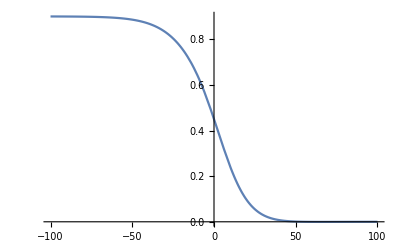

0.45

```mathematica
dens2=1/(c^3 (1+ⅇ^((qp z ᾱ)/(c (qm+qp))))^2 (qm+qp)^3 α)ᾱ (c^3 (1+ⅇ^((qp z ᾱ)/(c (qm+qp)))) (qm+qp)^3+c ⅇ^((qp z ᾱ)/(c (qm+qp))) qm (qm+qp) (c^2 Log[2]+Dv qp Log[4]-(c^2+2 Dv qp) Log[1+ⅇ^((qp z ᾱ)/(c (qm+qp)))]) ᾱ+Dv ⅇ^((qp z ᾱ)/(c (qm+qp))) qm qp^2 z (ᾱ)^2);
α=1;
Dv=25;
qp=20;
qm=20;
μ=0.1;
ᾱ=α-μ;
c=4.74342;

Plot[dens2,{z,-100,100}]
z=0;
dens2 (*Should equal 1/2*(1-μ/α)*)
Quit[]
```

### Comparing dens2 with dens1

α-μ

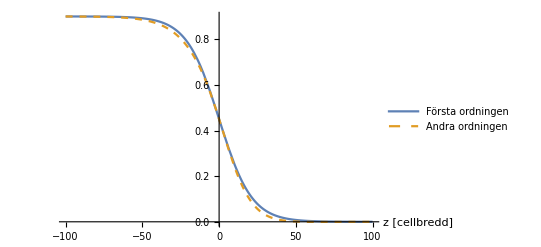

```mathematica
ᾱ=α-μ
dens1=(ᾱ)/(α+ⅇ^((qp z ᾱ)/(c (qm+qp))) α);
dens2=1/(c^3 (1+ⅇ^((qp z ᾱ)/(c (qm+qp))))^2 (qm+qp)^3 α)ᾱ (c^3 (1+ⅇ^((qp z ᾱ)/(c (qm+qp)))) (qm+qp)^3+c ⅇ^((qp z ᾱ)/(c (qm+qp))) qm (qm+qp) (c^2 Log[2]+Dv qp Log[4]-(c^2+2 Dv qp) Log[1+ⅇ^((qp z ᾱ)/(c (qm+qp)))]) ᾱ+Dv ⅇ^((qp z ᾱ)/(c (qm+qp))) qm qp^2 z (ᾱ)^2);
c=Sqrt[Dv*(α-μ)/(1-(α-μ)/(3*qp))];

α=1;
Dv=25;
qp=20;
qm=20;
μ=0.1;
Plot[{dens1,dens2},{z,-100,100},
AxesLabel->{"z [cellbredd]",""},
PlotStyle->{,Dashed},
PlotLegends->{"Första ordningen","Andra ordningen"}
]
Quit[]
```

### Testing parameters for slope plot and comparing with old shit

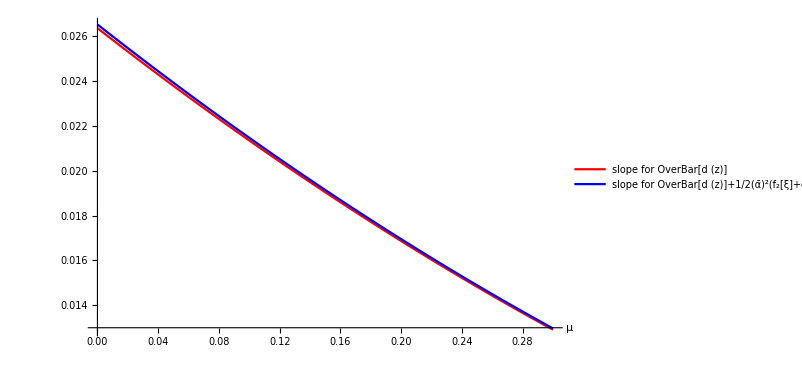

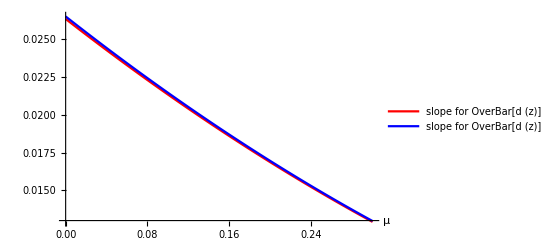

```mathematica
slope11=(qp (ᾱ)^2)/(4 c α(qm + qp ));

slope1122=(qp (ᾱ)^2 (2 (qm+qp)^2+qm ᾱ))/(8 c (qm+qp)^3 α);

α=1;
Dv=25;
qp=20;
qm=20;
(*μ=0.1;*)
ᾱ=α-μ;
c=4.74342;


Plot[{slope11,slope1122},{μ,0,0.3},PlotStyle->{Red,Blue},AxesLabel->Automatic,
PlotLegends->Placed[{"slope for OverBar[d (z)]","slope for OverBar[d (z)]+1/2(ᾱ)^2(f_2[ξ]+g_2[ξ])"},{0.7,0.6}]]


Plot[{slope11,slope1122},{μ,0,0.3},PlotStyle->{Red,Blue},AxesLabel->Automatic,
PlotLegends->LineLegend[{"slope for OverBar[d (z)]","slope for OverBar[d (z)]+1/2(ᾱ)^2(f_2[ξ]+g_2[ξ])"},LegendFunction->Frame,LabelStyle->{FontSize->20}]]

Quit[]
```